## 3 D Lattice Phonon

### Model - 3D

```mathematica
(*********************************************Function to generate spring between two points*********************************************)generateSpring[p1_,p2_,turns_,springRadius_,tubeRadius_]:=Module[{vector,length,direction,helixPath,alignmentMatrix},vector=p2-p1;
length=Norm[vector];
(*Handle the degenerate case where the points coincide*)If[length==0,Return[Graphics3D[]]];
direction=vector/length;(*Normalize the direction vector*)helixPath=Table[{springRadius Cos[2 Pi turns z/length],springRadius Sin[2 Pi turns z/length],z},{z,0,length,0.01}];(*Helical path along the z-axis*)alignmentMatrix=RotationMatrix3D[VectorAngle[{0,0,1},direction],Cross[{0,0,1},direction]];
helixPath=Map[alignmentMatrix.#+p1&,helixPath];(*Apply the alignment and translate the helix to p1*)Graphics3D[{Black,Tube[helixPath,tubeRadius]}]];

(*Rotation matrix in 3D for a given axis and angle*)
RotationMatrix3D[angle_,axis_]:=Module[{c=Cos[angle],s=Sin[angle],v=1-Cos[angle],x,y,z},{x,y,z}=Normalize[axis];
{{x x v+c,x y v-z s,x z v+y s},{x y v+z s,y y v+c,y z v-x s},{x z v-y s,y z v+x s,z z v+c}}];

(*********************************************Function to generate Lattice coordinates******************************************************)

cubicLatticeCoordinates[length_,width_,height_,ax_,ay_,az_]:=Module[{coordinates},coordinates=Table[{i*ax,j*ay,k*az},{i,0,length-1},{j,0,width-1},{k,0,height-1}];
Flatten[coordinates,2]];

(*********************************************Function to generate hoppings along x,y,and z directions*********************************************)

generateHoppings[coordinates_,ax_,ay_,az_]:=Module[{hoppings,neighbors,xHop,yHop,zHop,tx=1,ty=1,tz=1},
xHop={tx,{ax,0,0}};
yHop={ty,{0,ay,0}};
zHop={tz,{0,0,az}};
hoppings=Flatten[Table[neighbors={};
If[MemberQ[coordinates,coord+xHop[[2]]],AppendTo[neighbors,{coord,coord+xHop[[2]]}]];
If[MemberQ[coordinates,coord+yHop[[2]]],AppendTo[neighbors,{coord,coord+yHop[[2]]}]];
If[MemberQ[coordinates,coord+zHop[[2]]],AppendTo[neighbors,{coord,coord+zHop[[2]]}]];
neighbors,{coord,coordinates}],1];
hoppings];

(*******************************Parameters***********************************)

length=3;width=3;height=3;
ax=1;ay=1;az=1;
latticeCoordinates=SortBy[cubicLatticeCoordinates[length,width,height,ax,ay,az],First];
hoppings=generateHoppings[latticeCoordinates,ax,ay,az];

(*******************************Final Plot***********************************)

masses=Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[latticeCoordinates[[i]],0.2]},Boxed->False],{i,1,Length@latticeCoordinates}],ViewPoint->Above,ImageSize->700];
springs=Show[Table[generateSpring[hoppings[[i,1]],hoppings[[i,2]],8,0.05,0.01],{i,1,Length@hoppings}]];
label=Show[Table[Graphics3D[Text[Style[i,20,White],latticeCoordinates[[i]]]],{i,1,Length[latticeCoordinates]}]];
Show[masses,springs,label]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= ax&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=ax&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[latticeCoordinates];
NNHI=nearestNeighborsIndex[latticeCoordinates]
```

-Graphics3D-

{{1,{2,4,10}},{2,{1,3,5,11}},{3,{2,6,12}},{4,{1,5,7,13}},{5,{2,4,6,8,14}},{6,{3,5,9,15}},{7,{4,8,16}},{8,{5,7,9,17}},{9,{6,8,18}},{10,{1,11,13,19}},{11,{2,10,12,14,20}},{12,{3,11,15,21}},{13,{4,10,14,16,22}},{14,{5,11,13,15,17,23}},{15,{6,12,14,18,24}},{16,{7,13,17,25}},{17,{8,14,16,18,26}},{18,{9,15,17,27}},{19,{10,20,22}},{20,{11,19,21,23}},{21,{12,20,24}},{22,{13,19,23,25}},{23,{14,20,22,24,26}},{24,{15,21,23,27}},{25,{16,22,26}},{26,{17,23,25,27}},{27,{18,24,26}}}

### Transmission

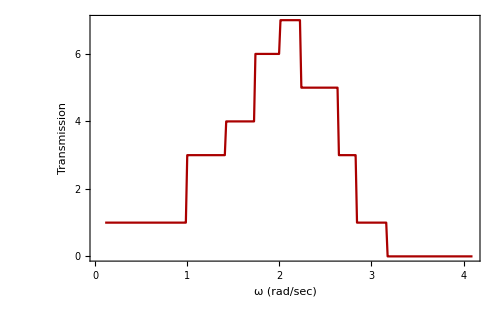

```mathematica
(****************************************** Parameters ********************************)
mChannel =1(*.12*); mSource=1(*.047*); mDrain=mSource;
mSC=(mChannel+mSource)/2; mCD = (mChannel+mDrain)/2;

kVerticalChannel = 1;kHorizontalChannel = 1(*13.7*);
kVerticalSource=1;kHorizontalSource= 1(*15.3*);
kVerticalDrain=kVerticalSource; kHorizontalDrain=kHorizontalSource;
kSC =1 (*15.3*)(*(kHorizontalChannel+kHorizontalSource)/2*); kCD = kSC (*(kHorizontalChannel+kHorizontalDrain)/2*);
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,9}];

(****************************************** dynamical Matrix ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
KChannel = Table[If[r==c,If[(MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]]) || (MemberQ[surfaceElements,r] &&  latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]]),kSC+Length@NNHI[[r,2]]*kHorizontalChannel,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@latticeCoordinates},{c, 1, Length@latticeCoordinates}];

(**********************************Couplings******************************************)
cSource = Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
cDrain = cSource;

(**********************************Leads******************************************)
αSource=Table[If[r==c,If[latticeCoordinates[[r,1]]==Min[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
αDrain=Table[If[r==c,If[latticeCoordinates[[r,1]]==Max[latticeCoordinates[[All,1]]],kSC+Length@NNHI[[r,2]]*kHorizontalSource,Length@NNHI[[r,2]]*kHorizontalChannel],If[MemberQ[NNHI[[r,2]],c],-kHorizontalChannel,0]],{r, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]},{c, Take[surfaceElements,-Floor[Length[surfaceElements]/2]]}];

βSource=Table[If[PossibleZeroQ[KChannel[[r,c+Max[surfaceElements1]]]],0,-kSC],{r,surfaceElements1},{c,surfaceElements1}];
βDrain=βSource;

Map[MatrixForm,{KChannel,cSource,αSource,αDrain,βSource}];

(************************************ Transmission Calculation ********************************************)
transmission=ParallelTable[
(**********************************Self energy for Source******************************************)
gS11=Inverse[(mSC ω1^2+ⅈ η) IdentityMatrix[Length@αSource]-αSource];
GS11=Array[x,{Length@αSource,Length@αSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[βSource].GS11.βSource-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αSource*Length@αSource}]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[cSource].Partition[Values[sol],{Length@cSource}].cSource,0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(**********************************Self energy for Drain******************************************)
gS11=Inverse[(mCD ω1^2+ⅈ η) IdentityMatrix[Length@αDrain]-αDrain];
GS11=Array[x,{Length@αDrain,Length@αDrain}]; (*Solve dyson equation*)
f=(gS11.βDrain.GS11.ConjugateTranspose[βDrain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@αDrain*Length@αDrain}]];
ΣD=ArrayFlatten[Table[If[i==j==Length@KChannel-(Length@surfaceElements1-1),cDrain.Partition[Values[sol],{Length@cDrain}].ConjugateTranspose[cDrain],0],{i,1,Length@KChannel-(Length@surfaceElements1-1)},{j,1,Length@KChannel-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*********************************Green's function & Transmission*************************************)
GR = Inverse[(mChannel IdentityMatrix[Length@KChannel] ω1^2 - KChannel -  ΣS-  ΣD )];
GA=ConjugateTranspose[GR];
{ω1,Chop[ Tr[ΓS.GR.ΓD.GA]]},{ω1,.11,4.1,.0151}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{6,1}]&;
ListLinePlot[transmission,BaseStyle->PointSize[.0001],PlotRange->(*{{-1.1,1.1},{-2.5,2.5}}*)All,PlotStyle-> Darker[Red],Axes->False,Frame-> True,FrameStyle->Directive[Black,20],FrameLabel->{Style["ω (rad/sec)",20,Black],Style["Transmission",20,Black]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->24,FontOpacity->0}),ImageSize->500]
```